```mathematica
Sum[1/j^3,{j,1,Infinity}]
```

Zeta[3]

```mathematica
Sum[1/j^2,{j,1,Infinity}]
```

π^2/6

```mathematica
Sum[1/j^4,{j,1,Infinity}]
```

π^4/90

```mathematica
Sum[1/(2 j - 1)^3,{j,1,Infinity}]
```

(7 Zeta[3])/8

```mathematica
Sum[(-1)^(j+1) 1/(2 j - 1)^3,{j,1,Infinity}]
```

π^3/32

```mathematica
Sum[(Mod[j,2]-Mod[j-1,2])/j,{j,1,Infinity}]
```

∑_(j=1)^∞ (-Mod[-1+j,2]+Mod[j,2])/j

```mathematica
FullSimplify[Mod[j,a]-Mod[j-1,a]]
```

-Mod[-1+j,a]+Mod[j,a]

```mathematica
N[(1+1/2-2/3)]
```

0.833333

```mathematica
N[(1/4+1/5-2/6)]
```

0.116667

```mathematica
N[(1/7+1/8-2/9)]
```

0.0456349

```mathematica
N[(1/10+1/11-2/12)]
```

0.0242424

```mathematica
504/6
```

84

```mathematica
504*5/60
```

42

```mathematica
504*5
```

2520

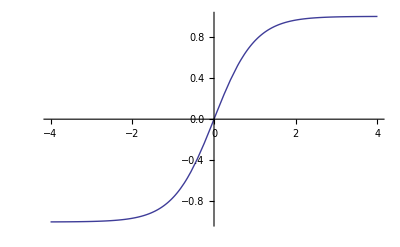

```mathematica
Plot[Tanh[x],{x,-4,4}]
```

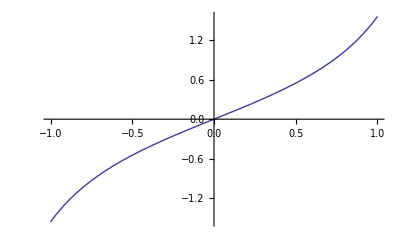

```mathematica
Plot[Tan[x],{x,-1,1}]
```

```mathematica
Tan[Pi/4]
```

1

```mathematica
Tanh[Pi/4]
```

Tanh[π/4]

```mathematica
Tan[Pi/4]
```

1

```mathematica
Tanh[I Pi/4]
```

ⅈ

```mathematica
ArcTanh[I]
```

(ⅈ π)/4

```mathematica
Series[ArcTanh[x],{x,0,20}]
```

x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15+x^17/17+x^19/19+O[x]^21

```mathematica
N[(ⅈ π)/4]
```

0.+0.785398 ⅈ

```mathematica
SS[x_] := x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15+x^17/17+x^19/19
```

```mathematica
N[SS[I]]
```

0.+0.76046 ⅈ

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcTanh[I]
```

(ⅈ π)/4

```mathematica
Series[ArcTan[x],{x,0,20}]
```

x-x^3/3+x^5/5-x^7/7+x^9/9-x^11/11+x^13/13-x^15/15+x^17/17-x^19/19+O[x]^21

```mathematica
Limit[HarmonicNumber[x]-HarmonicNumber[x/a],{x->Infinity}]
```

{Limit[HarmonicNumber[x]-HarmonicNumber[x/a],x→∞]}

```mathematica
CC[x_,a_]:=HarmonicNumber[x]- HarmonicNumber[Floor[x/a]]
```

```mathematica
N[CC[100000,6]]
```

1.79177

```mathematica
N[Log[6]]
```

1.79176

```mathematica
Etx[k_,t_]:=Sum[ (Mod[n,k]-Mod[n-1,k])/n,{n,1,t}]
```

```mathematica
N[Etx[6,100000]]
```

1.79177

```mathematica
Limit[HarmonicNumber[x]-HarmonicNumber[x/12],{x->Infinity}]
```

{Log[12]}